# Coexistence Equilibrium Without Buffelgrass

```mathematica
r1 =4.725;
k1=250;
b = .8;
γ= 1/35;
ϕ= .07;
k2 = (565+1350)/2;
μj = .042;
μa=1/140;
α1=.000001;
ρ=(1/(80-35))*(1/100)*.8;
ϵ=.113;
ω=.35;
k3=60000;
μb=1/3;
θj=1/(1111*250*(1-.0027));
θa=0.7/(1111*250*(1-.0027));
θt=0.63/(1111*250*(1-.0027));
σ=2.43175;
```

```mathematica
rd1 = (r1*γ)/(μa(μj +γ))
rd2 = (r1*γ)/((μa+α1)(μj +γ))
bigE = ϵ*μa/γ;
y = ((α1*ρ)/ϕ)*((ϵ/γ)-((b*k2*ρ)/(μa*ϕ*rd1)))(x^2) - (ϵ*((μa+α1)/γ)+((b*k2*ρ)/ϕ)(1-(1/rd2))+(k1+b*k2)*((α1*ρ)/(ϕ*μa*rd1))+1)x + (k1+b*k2)(1-(1/rd2));
```

267.814

267.776

```mathematica
rd1>(ρ*k2*b)/(bigE*ϕ)
rd2>1
ϕ>ρ
```

True

True

True

```mathematica
Solve[y==0]
```

{{x→341.225},{x→3.97549×10^8}}

```mathematica
ϕ/ρ
```

393.75

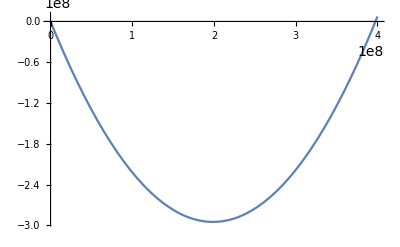

```mathematica
Plot[y,{x, 390,4*^8}]
```

```mathematica
nobuffelJ = ({{(-r1*ϵ*sa)/(k1+b*t)-(μj+γ), r1*(1-(ϵ*sj+2*sa)/(k1+b*t)), r1*b*sa*((ϵ*sj+sa)/(k1+b*t)^2)}, {γ, -μa - α1*(t/k2), -α1*(sa/k2)}, {0, -ϕ*σ*(t/k2), ϕ*(1-(2*t+σ*sa)/k2)}})
```

{{-0.405161,-1.36514,1.56874},{1/35,-0.00714367,-5.69786×10^-7},{0,-0.137911,-0.140416}}

```mathematica
sa = 341.22540
sj = ((μa+α1)/γ)*sa - ((α1*ρ)/(γ*ϕ))*sa^2
t = k2(1-(ρ/ϕ)*sa)
```

341.225

85.3079

127.726

```mathematica
nobuffelJ//FullSimplify//MatrixForm
```

(-0.405161 | -1.36514 | 1.56874
1/35 | -0.00714367 | -5.69786×10^-7
0 | -0.137911 | -0.140416)

```mathematica
Eigenvalues[nobuffelJ]
```

{-0.371522+0. ⅈ,-0.0905991+0.155772 ⅈ,-0.0905991-0.155772 ⅈ}

# Coexistence Equilibrium With Buffelgrass

```mathematica
β= 2857;
ûj = μj +β*θj;
ûa = μa + β*θa;
φ = 1-((θt*β)/ϕ);
β=  k3*(1-(μb/ω));
k4 = k2*φ;
ã1 = φ*α1;
```

```mathematica
rd3 = (r1*γ)/(ûa (ûj +γ))
rd4 = (r1*γ)/((ûa +ã1 )(ûj +γ))
bigE = ϵ*ûa /γ;
y = ((ã1 *ρ)/φ)*((ϵ/γ)-((b*k4 *ρ)/(ûa *φ*rd1)))(x^2) - (ϵ*((ûa +ã1 )/γ)+((b*k4 *ρ)/φ)(1-(1/rd2))+(k1+b*k4 )*((ã1 *ρ)/(φ*ûa *rd1))+1)x + (k1+b*k4 )(1-(1/rd2));
```

116.205

116.198

Conditions for existence

```mathematica
rd3>(ρ*k4*b)/(bigE*φ )
rd4>1
φ >ρ
```

True

True

True

```mathematica
Solve[y==0]
```

{{x→545.57},{x→8.57047×10^9}}

```mathematica
φ /ρ
```

5102.85

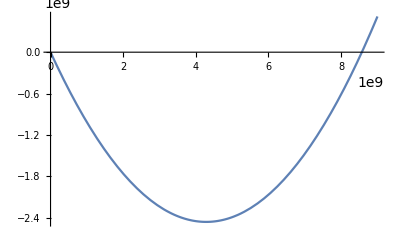

```mathematica
Plot[y,{x, 500,9*10^9}]
```

```mathematica
buffelJ = ({{(-r1*ϵ*sa)/(k1+b*t)-(ûj +γ), r1*(1-(ϵ*sj+2*sa)/(k1+b*t)), r1*b*sa*((ϵ*sj+sa)/(k1+b*t)^2)}, {γ, -ûa - ã1 *(t/k4), -ã1 *(sa/k4)}, {0, -φ*σ*(t/k4), φ*(1-(2*t+σ*sa)/k2)}})
```

{{-0.598201,-4.56036,3.64872},{1/35,-0.0143628,-3.56371×10^-7},{0,-0.324385,-0.121014}}

```mathematica
sa = 545.57
sj = ((ûa +ã1 )/γ)*sa - ((ã1 *ρ)/(γ*φ ))*sa^2
t = k4(1-(ρ/φ )*sa)
buf = k3*(1-(μb/ω))
```

545.57

274.271

775.75

2857.14

```mathematica
buffelJ//FullSimplify//MatrixForm
```

(-0.598201 | -4.56036 | 3.64872
1/35 | -0.0143628 | -3.56371×10^-7
0 | -0.324385 | -0.121014)

```mathematica
Eigenvalues[buffelJ]
```

{-0.510564+0. ⅈ,-0.111507+0.294482 ⅈ,-0.111507-0.294482 ⅈ}